```mathematica
BooleanTable[Xor[p, q], {p, q}]
```

{False,True,True,False}

```mathematica
b2i[b_]:=If[b, 1, 0]
bv2i[b_List]:=b2i/@b
```

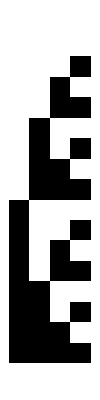

```mathematica
ArrayPlot[bv2i/@Table[BooleanTable[BooleanFunction[i, 2][p, q], {p, q}], {i, 0, 15}]]
```